```mathematica
<<Notation`
Symbolize[Subscript[N, 0]]
```

```mathematica
Symbolize[Subscript[N, 1,0]]
```

```mathematica
Symbolize[Subscript[N, 2,0]]
```

```mathematica
Symbolize[Subscript[N, 3,0]]
```

```mathematica
Symbolize[Subscript[N, 4,0]]
```

```mathematica
Symbolize[Subscript[N, 5,0]]
```

```mathematica
Symbolize[Subscript[N, 6,0]]
```

```mathematica
Symbolize[Subscript[N, 7,0]]
```

```mathematica
Symbolize[Subscript[N, 8,0]]
```

```mathematica
Symbolize[Subscript[N, 9,0]]
```

```mathematica
Symbolize[Subscript[N, 10,0]]
```

```mathematica
Symbolize[Subscript[N, 11,0]]
```

```mathematica
Symbolize[Subscript[N, 12,0]]
```

```mathematica
Subscript[N, 0] = {Subscript[N, 1,0], Subscript[N, 2,0], Subscript[N, 3,0], Subscript[N, 4,0], Subscript[N, 5,0], Subscript[N, 6,0], Subscript[N, 7,0], Subscript[N, 8,0], Subscript[N, 9,0], Subscript[N, 10,0], Subscript[N, 11,0], Subscript[N, 12,0]}
```

{N_(1,0),N_(2,0),N_(3,0),N_(4,0),N_(5,0),N_(6,0),N_(7,0),N_(8,0),N_(9,0),N_(10,0),N_(11,0),N_(12,0)}

```mathematica
Symbolize[Subscript[λ, 1]]
```

```mathematica
Symbolize[Subscript[λ, 2]]
```

```mathematica
Symbolize[Subscript[λ, 3]]
```

```mathematica
Symbolize[Subscript[λ, 4]]; Symbolize[Subscript[λ, 5]]
```

```mathematica
Symbolize[Subscript[λ, 6]]; Symbolize[Subscript[λ, 7]]; Symbolize[Subscript[λ, 8]]; Symbolize[Subscript[λ, 9]]; Symbolize[Subscript[λ, 10]]; Symbolize[Subscript[λ, 11]]; Symbolize[Subscript[λ, 12]]
```

```mathematica
Symbolize[Subscript[b, 9,β]]; Symbolize[Subscript[b, 9,α]]
```

```mathematica
m[s_]:= {{s+Subscript[λ, 1],0,0,0,0,0,0,0,0,0,0,0},{-Subscript[λ, 1],s+Subscript[λ, 2],0,0,0,0,0,0,0,0,0,0},{0,-Subscript[λ, 2],s+Subscript[λ, 3],0,0,0,0,0,0,0,0,0},{0,0,-Subscript[λ, 3],s+Subscript[λ, 4],0,0,0,0,0,0,0,0},{0,0,0,-Subscript[λ, 4], s+Subscript[λ, 5], 0,0,0,0,0,0,0}, {0,0,0,0, -Subscript[λ, 5], s+Subscript[λ, 6],0,0,0,0,0,0},{0,0,0,0,0,-Subscript[λ, 6], s+ Subscript[λ, 7],0,0,0,0,0},{0, 0, 0, 0, 0, 0, -Subscript[λ, 7], s+Subscript[λ, 8],0,0,0,0},{0,0,0,0,0,0,0,-Subscript[λ, 8], s+Subscript[λ, 9], 0, 0, 0}, {0,0,0,0,0,0,0,0,-Subscript[λ, 9]*Subscript[b, 9,β], s+Subscript[λ, 10],0,0},{0,0,0,0,0,0,0,0,-Subscript[λ, 9]*Subscript[b, 9,α],0,s+Subscript[λ, 11],0},{0,0,0,0,0,0,0,0,0,-Subscript[λ, 10],-Subscript[λ, 11],s}}
```

```mathematica
m[s]
```

{{s+λ_1,0,0,0,0,0,0,0,0,0,0,0},{-λ_1,s+λ_2,0,0,0,0,0,0,0,0,0,0},{0,-λ_2,s+λ_3,0,0,0,0,0,0,0,0,0},{0,0,-λ_3,s+λ_4,0,0,0,0,0,0,0,0},{0,0,0,-λ_4,s+λ_5,0,0,0,0,0,0,0},{0,0,0,0,-λ_5,s+λ_6,0,0,0,0,0,0},{0,0,0,0,0,-λ_6,s+λ_7,0,0,0,0,0},{0,0,0,0,0,0,-λ_7,s+λ_8,0,0,0,0},{0,0,0,0,0,0,0,-λ_8,s+λ_9,0,0,0},{0,0,0,0,0,0,0,0,-b_(9,β) λ_9,s+λ_10,0,0},{0,0,0,0,0,0,0,0,-b_(9,α) λ_9,0,s+λ_11,0},{0,0,0,0,0,0,0,0,0,-λ_10,-λ_11,s}}

```mathematica
MatrixForm[{{s+Subscript[λ, 1],0,0,0,0,0,0,0,0,0,0,0},{-Subscript[λ, 1],s+Subscript[λ, 2],0,0,0,0,0,0,0,0,0,0},{0,-Subscript[λ, 2],s+Subscript[λ, 3],0,0,0,0,0,0,0,0,0},{0,0,-Subscript[λ, 3],s+Subscript[λ, 4],0,0,0,0,0,0,0,0},{0,0,0,-Subscript[λ, 4], s+Subscript[λ, 5], 0,0,0,0,0,0,0}, {0,0,0,0, -Subscript[λ, 5], s+Subscript[λ, 6],0,0,0,0,0,0},{0,0,0,0,0,-Subscript[λ, 6], s+ Subscript[λ, 7],0,0,0,0,0},{0, 0, 0, 0, 0, 0, -Subscript[λ, 7], s+Subscript[λ, 8],0,0,0,0},{0,0,0,0,0,0,0,-Subscript[λ, 8], s+Subscript[λ, 9], 0, 0, 0}, {0,0,0,0,0,0,0,0,-Subscript[λ, 9]*Subscript[b, 9,β], s+Subscript[λ, 10],0,0},{0,0,0,0,0,0,0,0,-Subscript[λ, 9]*Subscript[b, 9,α],0,s+Subscript[λ, 11],0},{0,0,0,0,0,0,0,0,0,-Subscript[λ, 10],-Subscript[λ, 11],s}}]
```

(s+λ_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-λ_1 | s+λ_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -λ_2 | s+λ_3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -λ_3 | s+λ_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -λ_4 | s+λ_5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -λ_5 | s+λ_6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -λ_6 | s+λ_7 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -λ_7 | s+λ_8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ_8 | s+λ_9 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -b_(9,β) λ_9 | s+λ_10 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -b_(9,α) λ_9 | 0 | s+λ_11 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ_10 | -λ_11 | s)

```mathematica
invm[s_]:= Inverse[m[s]]
```

```mathematica
invm[s]
```

{{1/(s+λ_1),0,0,0,0,0,0,0,0,0,0,0},{λ_1/((s+λ_1) (s+λ_2)),1/(s+λ_2),0,0,0,0,0,0,0,0,0,0},{(λ_1 λ_2)/((s+λ_1) (s+λ_2) (s+λ_3)),λ_2/((s+λ_2) (s+λ_3)),1/(s+λ_3),0,0,0,0,0,0,0,0,0},{(λ_1 λ_2 λ_3)/((s+λ_1) (s+λ_2) (s+λ_3) (s+λ_4)),(λ_2 λ_3)/((s+λ_2) (s+λ_3) (s+λ_4)),λ_3/((s+λ_3) (s+λ_4)),1/(s+λ_4),0,0,0,0,0,0,0,0},{(λ_1 λ_2 λ_3 λ_4)/((s+λ_1) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5)),(λ_2 λ_3 λ_4)/((s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5)),(λ_3 λ_4)/((s+λ_3) (s+λ_4) (s+λ_5)),λ_4/((s+λ_4) (s+λ_5)),1/(s+λ_5),0,0,0,0,0,0,0},{(λ_1 λ_2 λ_3 λ_4 λ_5)/((s+λ_1) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6)),(λ_2 λ_3 λ_4 λ_5)/((s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6)),(λ_3 λ_4 λ_5)/((s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6)),(λ_4 λ_5)/((s+λ_4) (s+λ_5) (s+λ_6)),λ_5/((s+λ_5) (s+λ_6)),1/(s+λ_6),0,0,0,0,0,0},{(λ_1 λ_2 λ_3 λ_4 λ_5 λ_6)/((s+λ_1) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7)),(λ_2 λ_3 λ_4 λ_5 λ_6)/((s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7)),(λ_3 λ_4 λ_5 λ_6)/((s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7)),(λ_4 λ_5 λ_6)/((s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7)),(λ_5 λ_6)/((s+λ_5) (s+λ_6) (s+λ_7)),λ_6/((s+λ_6) (s+λ_7)),1/(s+λ_7),0,0,0,0,0},{(λ_1 λ_2 λ_3 λ_4 λ_5 λ_6 λ_7)/((s+λ_1) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8)),(λ_2 λ_3 λ_4 λ_5 λ_6 λ_7)/((s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8)),(λ_3 λ_4 λ_5 λ_6 λ_7)/((s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8)),(λ_4 λ_5 λ_6 λ_7)/((s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8)),(λ_5 λ_6 λ_7)/((s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8)),(λ_6 λ_7)/((s+λ_6) (s+λ_7) (s+λ_8)),λ_7/((s+λ_7) (s+λ_8)),1/(s+λ_8),0,0,0,0},{(λ_1 λ_2 λ_3 λ_4 λ_5 λ_6 λ_7 λ_8)/((s+λ_1) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(λ_2 λ_3 λ_4 λ_5 λ_6 λ_7 λ_8)/((s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(λ_3 λ_4 λ_5 λ_6 λ_7 λ_8)/((s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(λ_4 λ_5 λ_6 λ_7 λ_8)/((s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(λ_5 λ_6 λ_7 λ_8)/((s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(λ_6 λ_7 λ_8)/((s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(λ_7 λ_8)/((s+λ_7) (s+λ_8) (s+λ_9)),λ_8/((s+λ_8) (s+λ_9)),1/(s+λ_9),0,0,0},{(b_(9,β) λ_1 λ_2 λ_3 λ_4 λ_5 λ_6 λ_7 λ_8 λ_9)/((s+λ_1) (s+λ_10) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,β) λ_2 λ_3 λ_4 λ_5 λ_6 λ_7 λ_8 λ_9)/((s+λ_10) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,β) λ_3 λ_4 λ_5 λ_6 λ_7 λ_8 λ_9)/((s+λ_10) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,β) λ_4 λ_5 λ_6 λ_7 λ_8 λ_9)/((s+λ_10) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,β) λ_5 λ_6 λ_7 λ_8 λ_9)/((s+λ_10) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,β) λ_6 λ_7 λ_8 λ_9)/((s+λ_10) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,β) λ_7 λ_8 λ_9)/((s+λ_10) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,β) λ_8 λ_9)/((s+λ_10) (s+λ_8) (s+λ_9)),(b_(9,β) λ_9)/((s+λ_10) (s+λ_9)),1/(s+λ_10),0,0},{(b_(9,α) λ_1 λ_2 λ_3 λ_4 λ_5 λ_6 λ_7 λ_8 λ_9)/((s+λ_1) (s+λ_11) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,α) λ_2 λ_3 λ_4 λ_5 λ_6 λ_7 λ_8 λ_9)/((s+λ_11) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,α) λ_3 λ_4 λ_5 λ_6 λ_7 λ_8 λ_9)/((s+λ_11) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,α) λ_4 λ_5 λ_6 λ_7 λ_8 λ_9)/((s+λ_11) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,α) λ_5 λ_6 λ_7 λ_8 λ_9)/((s+λ_11) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,α) λ_6 λ_7 λ_8 λ_9)/((s+λ_11) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,α) λ_7 λ_8 λ_9)/((s+λ_11) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,α) λ_8 λ_9)/((s+λ_11) (s+λ_8) (s+λ_9)),(b_(9,α) λ_9)/((s+λ_11) (s+λ_9)),0,1/(s+λ_11),0},{(λ_1 λ_2 λ_3 λ_4 λ_5 λ_6 λ_7 λ_8 (b_(9,β) s λ_10 λ_9+b_(9,α) s λ_11 λ_9+b_(9,α) λ_10 λ_11 λ_9+b_(9,β) λ_10 λ_11 λ_9))/(s (s+λ_1) (s+λ_10) (s+λ_11) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(λ_2 λ_3 λ_4 λ_5 λ_6 λ_7 λ_8 (b_(9,β) s λ_10 λ_9+b_(9,α) s λ_11 λ_9+b_(9,α) λ_10 λ_11 λ_9+b_(9,β) λ_10 λ_11 λ_9))/(s (s+λ_10) (s+λ_11) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(λ_3 λ_4 λ_5 λ_6 λ_7 λ_8 (b_(9,β) s λ_10 λ_9+b_(9,α) s λ_11 λ_9+b_(9,α) λ_10 λ_11 λ_9+b_(9,β) λ_10 λ_11 λ_9))/(s (s+λ_10) (s+λ_11) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(λ_4 λ_5 λ_6 λ_7 λ_8 (b_(9,β) s λ_10 λ_9+b_(9,α) s λ_11 λ_9+b_(9,α) λ_10 λ_11 λ_9+b_(9,β) λ_10 λ_11 λ_9))/(s (s+λ_10) (s+λ_11) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(λ_5 λ_6 λ_7 λ_8 (b_(9,β) s λ_10 λ_9+b_(9,α) s λ_11 λ_9+b_(9,α) λ_10 λ_11 λ_9+b_(9,β) λ_10 λ_11 λ_9))/(s (s+λ_10) (s+λ_11) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(λ_6 λ_7 λ_8 (b_(9,β) s λ_10 λ_9+b_(9,α) s λ_11 λ_9+b_(9,α) λ_10 λ_11 λ_9+b_(9,β) λ_10 λ_11 λ_9))/(s (s+λ_10) (s+λ_11) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(λ_7 λ_8 (b_(9,β) s λ_10 λ_9+b_(9,α) s λ_11 λ_9+b_(9,α) λ_10 λ_11 λ_9+b_(9,β) λ_10 λ_11 λ_9))/(s (s+λ_10) (s+λ_11) (s+λ_7) (s+λ_8) (s+λ_9)),(λ_8 (b_(9,β) s λ_10 λ_9+b_(9,α) s λ_11 λ_9+b_(9,α) λ_10 λ_11 λ_9+b_(9,β) λ_10 λ_11 λ_9))/(s (s+λ_10) (s+λ_11) (s+λ_8) (s+λ_9)),(b_(9,β) s λ_10 λ_9+b_(9,α) s λ_11 λ_9+b_(9,α) λ_10 λ_11 λ_9+b_(9,β) λ_10 λ_11 λ_9)/(s (s+λ_10) (s+λ_11) (s+λ_9)),λ_10/(s (s+λ_10)),(-b_(9,β) (s+λ_1) λ_10 (s+λ_11) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) λ_9 (s+λ_9)-(s+λ_1) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9) (-b_(9,α) (s+λ_10) λ_11 λ_9-b_(9,β) λ_10 (s+λ_11) λ_9))/(b_(9,α) s (s+λ_1) (s+λ_10) (s+λ_11) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) λ_9 (s+λ_9)),1/s}}

```mathematica
Simplify[invm[s]]
```

{{1/(s+λ_1),0,0,0,0,0,0,0,0,0,0,0},{λ_1/((s+λ_1) (s+λ_2)),1/(s+λ_2),0,0,0,0,0,0,0,0,0,0},{(λ_1 λ_2)/((s+λ_1) (s+λ_2) (s+λ_3)),λ_2/((s+λ_2) (s+λ_3)),1/(s+λ_3),0,0,0,0,0,0,0,0,0},{(λ_1 λ_2 λ_3)/((s+λ_1) (s+λ_2) (s+λ_3) (s+λ_4)),(λ_2 λ_3)/((s+λ_2) (s+λ_3) (s+λ_4)),λ_3/((s+λ_3) (s+λ_4)),1/(s+λ_4),0,0,0,0,0,0,0,0},{(λ_1 λ_2 λ_3 λ_4)/((s+λ_1) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5)),(λ_2 λ_3 λ_4)/((s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5)),(λ_3 λ_4)/((s+λ_3) (s+λ_4) (s+λ_5)),λ_4/((s+λ_4) (s+λ_5)),1/(s+λ_5),0,0,0,0,0,0,0},{(λ_1 λ_2 λ_3 λ_4 λ_5)/((s+λ_1) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6)),(λ_2 λ_3 λ_4 λ_5)/((s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6)),(λ_3 λ_4 λ_5)/((s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6)),(λ_4 λ_5)/((s+λ_4) (s+λ_5) (s+λ_6)),λ_5/((s+λ_5) (s+λ_6)),1/(s+λ_6),0,0,0,0,0,0},{(λ_1 λ_2 λ_3 λ_4 λ_5 λ_6)/((s+λ_1) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7)),(λ_2 λ_3 λ_4 λ_5 λ_6)/((s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7)),(λ_3 λ_4 λ_5 λ_6)/((s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7)),(λ_4 λ_5 λ_6)/((s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7)),(λ_5 λ_6)/((s+λ_5) (s+λ_6) (s+λ_7)),λ_6/((s+λ_6) (s+λ_7)),1/(s+λ_7),0,0,0,0,0},{(λ_1 λ_2 λ_3 λ_4 λ_5 λ_6 λ_7)/((s+λ_1) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8)),(λ_2 λ_3 λ_4 λ_5 λ_6 λ_7)/((s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8)),(λ_3 λ_4 λ_5 λ_6 λ_7)/((s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8)),(λ_4 λ_5 λ_6 λ_7)/((s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8)),(λ_5 λ_6 λ_7)/((s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8)),(λ_6 λ_7)/((s+λ_6) (s+λ_7) (s+λ_8)),λ_7/((s+λ_7) (s+λ_8)),1/(s+λ_8),0,0,0,0},{(λ_1 λ_2 λ_3 λ_4 λ_5 λ_6 λ_7 λ_8)/((s+λ_1) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(λ_2 λ_3 λ_4 λ_5 λ_6 λ_7 λ_8)/((s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(λ_3 λ_4 λ_5 λ_6 λ_7 λ_8)/((s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(λ_4 λ_5 λ_6 λ_7 λ_8)/((s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(λ_5 λ_6 λ_7 λ_8)/((s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(λ_6 λ_7 λ_8)/((s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(λ_7 λ_8)/((s+λ_7) (s+λ_8) (s+λ_9)),λ_8/((s+λ_8) (s+λ_9)),1/(s+λ_9),0,0,0},{(b_(9,β) λ_1 λ_2 λ_3 λ_4 λ_5 λ_6 λ_7 λ_8 λ_9)/((s+λ_1) (s+λ_10) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,β) λ_2 λ_3 λ_4 λ_5 λ_6 λ_7 λ_8 λ_9)/((s+λ_10) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,β) λ_3 λ_4 λ_5 λ_6 λ_7 λ_8 λ_9)/((s+λ_10) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,β) λ_4 λ_5 λ_6 λ_7 λ_8 λ_9)/((s+λ_10) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,β) λ_5 λ_6 λ_7 λ_8 λ_9)/((s+λ_10) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,β) λ_6 λ_7 λ_8 λ_9)/((s+λ_10) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,β) λ_7 λ_8 λ_9)/((s+λ_10) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,β) λ_8 λ_9)/((s+λ_10) (s+λ_8) (s+λ_9)),(b_(9,β) λ_9)/((s+λ_10) (s+λ_9)),1/(s+λ_10),0,0},{(b_(9,α) λ_1 λ_2 λ_3 λ_4 λ_5 λ_6 λ_7 λ_8 λ_9)/((s+λ_1) (s+λ_11) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,α) λ_2 λ_3 λ_4 λ_5 λ_6 λ_7 λ_8 λ_9)/((s+λ_11) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,α) λ_3 λ_4 λ_5 λ_6 λ_7 λ_8 λ_9)/((s+λ_11) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,α) λ_4 λ_5 λ_6 λ_7 λ_8 λ_9)/((s+λ_11) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,α) λ_5 λ_6 λ_7 λ_8 λ_9)/((s+λ_11) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,α) λ_6 λ_7 λ_8 λ_9)/((s+λ_11) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,α) λ_7 λ_8 λ_9)/((s+λ_11) (s+λ_7) (s+λ_8) (s+λ_9)),(b_(9,α) λ_8 λ_9)/((s+λ_11) (s+λ_8) (s+λ_9)),(b_(9,α) λ_9)/((s+λ_11) (s+λ_9)),0,1/(s+λ_11),0},{(λ_1 (b_(9,α) (s+λ_10) λ_11+b_(9,β) λ_10 (s+λ_11)) λ_2 λ_3 λ_4 λ_5 λ_6 λ_7 λ_8 λ_9)/(s (s+λ_1) (s+λ_10) (s+λ_11) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),((b_(9,α) (s+λ_10) λ_11+b_(9,β) λ_10 (s+λ_11)) λ_2 λ_3 λ_4 λ_5 λ_6 λ_7 λ_8 λ_9)/(s (s+λ_10) (s+λ_11) (s+λ_2) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),((b_(9,α) (s+λ_10) λ_11+b_(9,β) λ_10 (s+λ_11)) λ_3 λ_4 λ_5 λ_6 λ_7 λ_8 λ_9)/(s (s+λ_10) (s+λ_11) (s+λ_3) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),((b_(9,α) (s+λ_10) λ_11+b_(9,β) λ_10 (s+λ_11)) λ_4 λ_5 λ_6 λ_7 λ_8 λ_9)/(s (s+λ_10) (s+λ_11) (s+λ_4) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),((b_(9,α) (s+λ_10) λ_11+b_(9,β) λ_10 (s+λ_11)) λ_5 λ_6 λ_7 λ_8 λ_9)/(s (s+λ_10) (s+λ_11) (s+λ_5) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),((b_(9,α) (s+λ_10) λ_11+b_(9,β) λ_10 (s+λ_11)) λ_6 λ_7 λ_8 λ_9)/(s (s+λ_10) (s+λ_11) (s+λ_6) (s+λ_7) (s+λ_8) (s+λ_9)),((b_(9,α) (s+λ_10) λ_11+b_(9,β) λ_10 (s+λ_11)) λ_7 λ_8 λ_9)/(s (s+λ_10) (s+λ_11) (s+λ_7) (s+λ_8) (s+λ_9)),((b_(9,α) (s+λ_10) λ_11+b_(9,β) λ_10 (s+λ_11)) λ_8 λ_9)/(s (s+λ_10) (s+λ_11) (s+λ_8) (s+λ_9)),((b_(9,α) (s+λ_10) λ_11+b_(9,β) λ_10 (s+λ_11)) λ_9)/(s (s+λ_10) (s+λ_11) (s+λ_9)),λ_10/(s (s+λ_10)),λ_11/(s^2+s λ_11),1/s}}

```mathematica
R[s_]:=invm[s].Subscript[N, 0]
```

```mathematica
R[s][[1]]
```

(N_(1,0))/(s+λ_1)

```mathematica
R[5][[1]]
```

(N_(1,0))/(5+λ_1)

```mathematica
InverseLaplaceTransform[R[s][[1]],s,t]
```

ⅇ^(-t λ_1) N_(1,0)

```mathematica
x[s_]:=Simplify[R[s][[2]]]
```

```mathematica
Simplify[InverseLaplaceTransform[x[s],s,t]]
```

(ⅇ^(-t (λ_1+λ_2)) (-ⅇ^(t λ_2) N_(1,0) λ_1+ⅇ^(t λ_1) (N_(1,0) λ_1+N_(2,0) (λ_1-λ_2))))/(λ_1-λ_2)

```mathematica
Symbolize[Subscript[N, 0,1]]
```

```mathematica
Subscript[N, 0,1] = {1,0,0,0,0,0,0,0,0,0,0,0}
```

{1,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
R0[s_]:=invm[s].Subscript[N, 0,1]
```

```mathematica
N1[s_]:=Simplify[R0[s][[1]]]
```

```mathematica
Simplify[InverseLaplaceTransform[N1[s],s,t]]
```

ⅇ^(-t λ_1)

```mathematica
N2[s_]:=Simplify[R0[s][[2]]]
```

```mathematica
Simplify[InverseLaplaceTransform[N2[s],s,t]]
```

-((ⅇ^(-t λ_1)-ⅇ^(-t λ_2)) λ_1)/(λ_1-λ_2)

```mathematica
Manipulate[Plot[-((ⅇ^(-t Subscript[λ, 1])-ⅇ^(-t Subscript[λ, 2])) Subscript[λ, 1])/(Subscript[λ, 1]-Subscript[λ, 2]),{t,0.,10.}],{Subscript[λ, 1],1/1000,1/10},{Subscript[λ, 2],1/5,1/2}]
```

```mathematica
p2[a_,b_] := LogPlot[-((Exp[-t*a]-Exp[-t*b])a)/(a-b),{t,0.,10.},PlotRange->Automatic,PlotStyle->Blue];
```

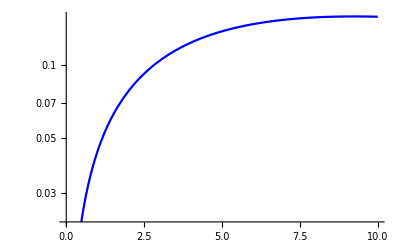

```mathematica
p2[0.05,1/5]
```

```mathematica
p1[a_,b_] := LogPlot[Exp[-t*a],{t,0.,10.},PlotRange->Automatic,PlotStyle->Red];
```

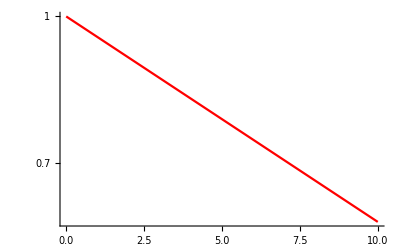

```mathematica
p1[0.05,1/5]
```

```mathematica
Manipulate[Show[p1[a,b],p2[a,b],PlotRange->Automatic],{a,1/1000,1/10},{b,1/5,1/2}]
```

```mathematica
N3[s_]:=Simplify[R0[s][[3]]]
```

```mathematica
Simplify[InverseLaplaceTransform[N3[s],s,t]]
```

(ⅇ^(-t (λ_1+λ_2+λ_3)) λ_1 λ_2 (ⅇ^(t (λ_1+λ_2)) (λ_1-λ_2)+ⅇ^(t (λ_2+λ_3)) (λ_2-λ_3)+ⅇ^(t (λ_1+λ_3)) (-λ_1+λ_3)))/((λ_1-λ_2) (λ_1-λ_3) (λ_2-λ_3))

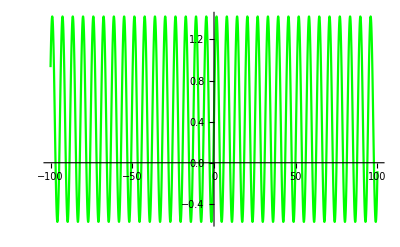

```mathematica
H1[b_,c_]:=Plot[Sin[x/b]+Cos[12 c],{x,-100,100},PlotStyle->Green]
H1[1,2]
```